```mathematica
A=208; (*Pb*)
Subscript[r, 0]=(1.12 A^(1/3)-0.86 A^(-1/3));(*fm*)
a=0.54 ;(*fm*)
Subscript[ρ, 0]=0.17;(*fm^-3*);
Subscript[σ, inel]=3;
ws[s_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s^2+z^2)-Subscript[r, 0])/a]));
ws1[s1_,s2_,ang_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-Subscript[r, 0])/a]));
```

```mathematica
NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}]
```

1.00017

```mathematica
T[s_]:=NIntegrate[ws[s,z],{z,-∞,∞}]
T1[s1_,s2_,ang_]:=NIntegrate[ws1[s1,s2,ang,z],{z,-∞,∞}]
```

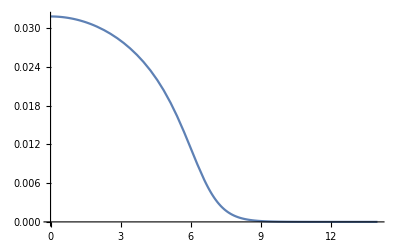

```mathematica
Plot[Subscript[σ, inel] T[x],{x,0,14}]
```

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

1.00017

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-Subscript[σ, inel] T[s])^A),{s,0,∞},{ang,0,2 π}]]
```

```mathematica
NpartTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NpartTab];
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
ParallelDo[NpartTab[[i,2]]=Npart[NpartTab[[i,1]]],{i,Length[NpartTab]}]
```

```mathematica
NpartTab
```

{{0.,392.107},{0.1,392.038},{0.2,391.822},{0.3,391.486},{0.4,391.005},{0.5,390.386},{0.6,389.632},{0.7,388.743},{0.8,387.721},{0.9,386.566},{1.,385.28},{1.1,383.865},{1.2,382.323},{1.3,380.657},{1.4,378.867},{1.5,376.958},{1.6,374.931},{1.7,372.79},{1.8,370.537},{1.9,368.175},{2.,365.709},{2.5,351.914},{3.,335.995},{3.5,318.371},{4.,299.43},{4.5,279.518},{5.,258.943},{5.5,237.977},{6.,216.867},{6.5,195.836},{7.,175.092},{7.5,154.827},{8.,135.225},{8.5,116.457},{9.,98.6913},{9.5,82.0856},{10.,66.7929},{10.5,52.958},{11.,40.7145},{11.5,30.1767},{12.,21.4244},{12.1,19.8914},{12.2,18.4306},{12.3,17.0418},{12.4,15.7243},{12.5,14.4775},{12.6,13.3003},{12.7,12.1918},{12.8,11.1507},{12.9,10.1754},{13.,9.26422},{13.1,8.4154},{13.2,7.62688},{13.3,6.89648},{13.4,6.22186},{13.5,5.6006},{13.6,5.03013},{13.7,4.50783},{13.8,4.03101},{13.9,3.59697},{14.,3.20298},{14.1,2.84635},{14.2,2.52443},{14.3,2.23462},{14.4,1.97437},{14.5,1.74128},{14.6,1.53303},{14.7,1.34741},{14.8,1.18234},{14.9,1.03588},{15.,0.906192}}

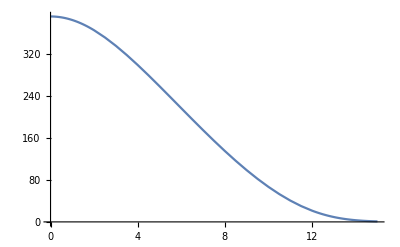

```mathematica
ListPlot[NpartTab,Joined->True]
```

```mathematica
Npartinter=Interpolation[NpartTab];
```

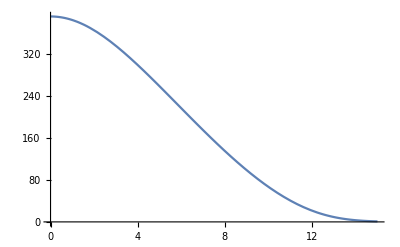

```mathematica
Plot[Npartinter[x],{x,0,15}]
```